```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.1,Jtwo,0.3,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.8426149773176358}]
```

{z→0.842615}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.1,l->0.3}
```

0.842615+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
p= Check[FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
],z->0];
AppendTo[lst,{Jtwoo,p}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.8426149773176358]]
```

{{0.005,0.845429},{0.01,0.847974},{0.015,0.850233},{0.02,0.852192},{0.025,0.853835},{0.03,0.855149},{0.035,0.856125},{0.04,0.856754},{0.045,0.857032},{0.05,0.856957},{0.055,0.856531},{0.06,0.85576},{0.065,0.854652},{0.07,0.853217},{0.075,0.851469},{0.08,0.849423},{0.085,0.847092},{0.09,0.844494},{0.095,0.841644},{0.1,0.838558}}

```mathematica
moduler[Lister[-1,-0.005,0.8426149773176358]]
```

{{-0.005,0.839548},{-0.01,0.836244},{-0.015,0.832718},{-0.02,0.828986},{-0.025,0.82506},{-0.03,0.820954},{-0.035,0.816679},{-0.04,0.812245},{-0.045,0.807663},{-0.05,0.80294},{-0.055,0.798086},{-0.06,0.793105},{-0.065,0.788005},{-0.07,0.78279},{-0.075,0.777466},{-0.08,0.772036},{-0.085,0.766505},{-0.09,0.760874},{-0.095,0.755147},{-0.1,0.749325}}

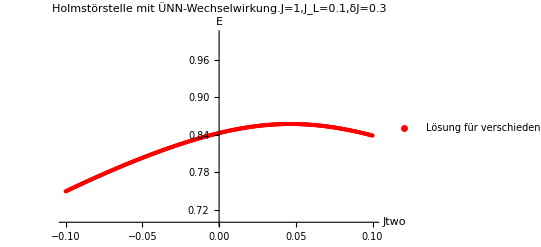

```mathematica
G =ListPlot[Fueger[moduler[Lister[1,0.0005,0.84261497731176358]],moduler[Lister[-1,-0.0005,0.84261497731176358]]],AxesLabel->{Jtwo,"E"},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=0.3",PlotRange->{0.7,1},PlotStyle->Red]
```

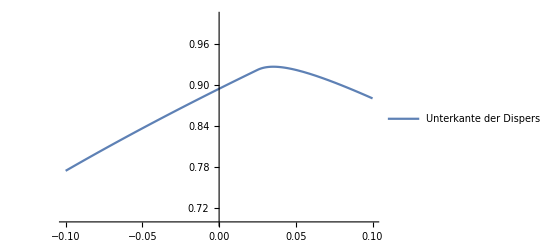

```mathematica
P =Plot[Sqrt[1+2(0.1*Cos[Inv[0.1,Jtwo]]+Jtwo*Cos[2*Inv[0.1,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.7,1},PlotLegends->{"Unterkante der Dispersion"}]
```

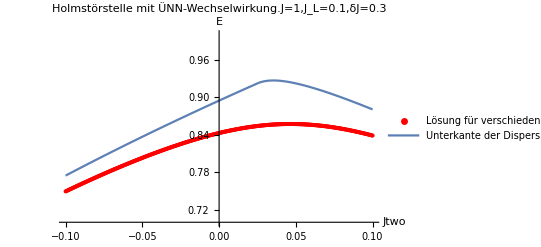

```mathematica
Show[G,P]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.1,moduler[Lister[-1,-0.005,0.8426149773176358]]]
```

{{-0.005,0.0492715},{-0.01,0.0469321},{-0.015,0.044778},{-0.02,0.0427938},{-0.025,0.0409652},{-0.03,0.0392786},{-0.035,0.0377216},{-0.04,0.0362829},{-0.045,0.034952},{-0.05,0.0337195},{-0.055,0.0325768},{-0.06,0.0315162},{-0.065,0.0305306},{-0.07,0.0296137},{-0.075,0.0287597},{-0.08,0.0279636},{-0.085,0.0272208},{-0.09,0.0265269},{-0.095,0.0258784},{-0.1,0.0252717}}

```mathematica
differ[1,0.1,moduler[Lister[1,0.005,0.8426149773176358]]]
```

{{0.005,0.054571},{0.01,0.0575647},{0.015,0.0608102},{0.02,0.0643236},{0.025,0.264199},{0.03,0.0704137},{0.035,0.0704662},{0.04,0.0692587},{0.045,0.0673296},{0.05,0.0649974},{0.055,0.0624603},{0.06,0.0598454},{0.065,0.0572356},{0.07,0.0546846},{0.075,0.0522268},{0.08,0.0498828},{0.085,0.0476638},{0.09,0.0455745},{0.095,0.0436152},{0.1,0.0417828}}

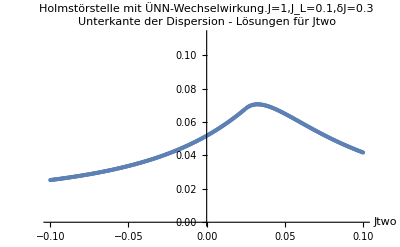

```mathematica
ListPlot[Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,0.8426149773176358]]],differ[1,0.1,moduler[Lister[1,0.0005,0.8426149773176358]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=0.3"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.87141}. NIntegrate obtained -0.179235 and 0.277837 for the integral and error estimates.

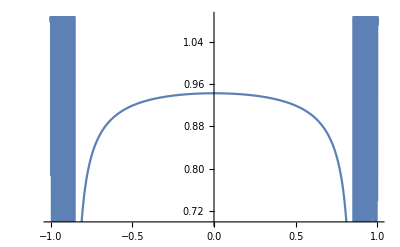

```mathematica
Plot[NullsHolm[-0.035,z],{z,-1,1}]
```

```mathematica
Fueger[moduler[Lister[1,0.0005,0.84261497731176358]],moduler[Lister[-1,-0.0005,0.84261497731176358]]]
```

{{0.0005,0.842908},{0.001,0.843199},{0.0015,0.843486},{0.002,0.843772},{0.0025,0.844055},{0.003,0.844335},{0.0035,0.844612},{0.004,0.844887},{0.0045,0.845159},{0.005,0.845429},{0.0055,0.845696},{0.006,0.84596},{0.0065,0.846221},{0.007,0.84648},{0.0075,0.846736},{0.008,0.846989},{0.0085,0.84724},{0.009,0.847487},{0.0095,0.847732},{0.01,0.847974},{0.0105,0.848213},{0.011,0.848449},{0.0115,0.848682},{0.012,0.848913},{0.0125,0.84914},{0.013,0.849365},{0.0135,0.849586},{0.014,0.849805},{0.0145,0.850021},{0.015,0.850233},{0.0155,0.850443},{0.016,0.850649},{0.0165,0.850853},{0.017,0.851053},{0.0175,0.851251},{0.018,0.851445},{0.0185,0.851637},{0.019,0.851825},{0.0195,0.85201},{0.02,0.852192},{0.0205,0.85237},{0.021,0.852546},{0.0215,0.852718},{0.022,0.852887},{0.0225,0.853053},{0.023,0.853216},{0.0235,0.853376},{0.024,0.853532},{0.0245,0.853685},{0.025,0.853835},{0.0255,0.853981},{0.026,0.854124},{0.0265,0.854264},{0.027,0.8544},{0.0275,0.854534},{0.028,0.854663},{0.0285,0.85479},{0.029,0.854913},{0.0295,0.855033},{0.03,0.855149},{0.0305,0.855262},{0.031,0.855372},{0.0315,0.855478},{0.032,0.855581},{0.0325,0.85568},{0.033,0.855776},{0.0335,0.855868},{0.034,0.855957},{0.0345,0.856043},{0.035,0.856125},{0.0355,0.856204},{0.036,0.856279},{0.0365,0.856351},{0.037,0.856419},{0.0375,0.856483},{0.038,0.856545},{0.0385,0.856602},{0.039,0.856656},{0.0395,0.856707},{0.04,0.856754},{0.0405,0.856798},{0.041,0.856838},{0.0415,0.856875},{0.042,0.856908},{0.0425,0.856937},{0.043,0.856963},{0.0435,0.856986},{0.044,0.857005},{0.0445,0.85702},{0.045,0.857032},{0.0455,0.85704},{0.046,0.857045},{0.0465,0.857047},{0.047,0.857044},{0.0475,0.857039},{0.048,0.857029},{0.0485,0.857017},{0.049,0.857},{0.0495,0.85698},{0.05,0.856957},{0.0505,0.85693},{0.051,0.8569},{0.0515,0.856866},{0.052,0.856829},{0.0525,0.856788},{0.053,0.856743},{0.0535,0.856696},{0.054,0.856644},{0.0545,0.85659},{0.055,0.856531},{0.0555,0.85647},{0.056,0.856404},{0.0565,0.856336},{0.057,0.856264},{0.0575,0.856188},{0.058,0.85611},{0.0585,0.856027},{0.059,0.855942},{0.0595,0.855853},{0.06,0.85576},{0.0605,0.855664},{0.061,0.855565},{0.0615,0.855463},{0.062,0.855357},{0.0625,0.855247},{0.063,0.855135},{0.0635,0.855019},{0.064,0.8549},{0.0645,0.854777},{0.065,0.854652},{0.0655,0.854523},{0.066,0.854391},{0.0665,0.854255},{0.067,0.854116},{0.0675,0.853974},{0.068,0.853829},{0.0685,0.853681},{0.069,0.85353},{0.0695,0.853375},{0.07,0.853217},{0.0705,0.853056},{0.071,0.852892},{0.0715,0.852725},{0.072,0.852555},{0.0725,0.852382},{0.073,0.852205},{0.0735,0.852026},{0.074,0.851843},{0.0745,0.851658},{0.075,0.851469},{0.0755,0.851278},{0.076,0.851083},{0.0765,0.850886},{0.077,0.850686},{0.0775,0.850482},{0.078,0.850276},{0.0785,0.850067},{0.079,0.849855},{0.0795,0.84964},{0.08,0.849423},{0.0805,0.849202},{0.081,0.848979},{0.0815,0.848752},{0.082,0.848524},{0.0825,0.848292},{0.083,0.848057},{0.0835,0.84782},{0.084,0.84758},{0.0845,0.847338},{0.085,0.847092},{0.0855,0.846844},{0.086,0.846594},{0.0865,0.84634},{0.087,0.846084},{0.0875,0.845826},{0.088,0.845564},{0.0885,0.845301},{0.089,0.845034},{0.0895,0.844766},{0.09,0.844494},{0.0905,0.84422},{0.091,0.843944},{0.0915,0.843665},{0.092,0.843384},{0.0925,0.8431},{0.093,0.842813},{0.0935,0.842525},{0.094,0.842234},{0.0945,0.84194},{0.095,0.841644},{0.0955,0.841346},{0.096,0.841045},{0.0965,0.840742},{0.097,0.840437},{0.0975,0.84013},{0.098,0.83982},{0.0985,0.839508},{0.099,0.839193},{0.0995,0.838877},{0.1,0.838558},{-0.0005,0.842319},{-0.001,0.842021},{-0.0015,0.841721},{-0.002,0.841418},{-0.0025,0.841112},{-0.003,0.840804},{-0.0035,0.840494},{-0.004,0.840181},{-0.0045,0.839866},{-0.005,0.839548},{-0.0055,0.839228},{-0.006,0.838906},{-0.0065,0.838581},{-0.007,0.838254},{-0.0075,0.837925},{-0.008,0.837593},{-0.0085,0.837259},{-0.009,0.836923},{-0.0095,0.836585},{-0.01,0.836244},{-0.0105,0.835901},{-0.011,0.835556},{-0.0115,0.835209},{-0.012,0.83486},{-0.0125,0.834508},{-0.013,0.834154},{-0.0135,0.833798},{-0.014,0.833441},{-0.0145,0.833081},{-0.015,0.832718},{-0.0155,0.832354},{-0.016,0.831988},{-0.0165,0.83162},{-0.017,0.831249},{-0.0175,0.830877},{-0.018,0.830503},{-0.0185,0.830127},{-0.019,0.829748},{-0.0195,0.829368},{-0.02,0.828986},{-0.0205,0.828602},{-0.021,0.828216},{-0.0215,0.827828},{-0.022,0.827438},{-0.0225,0.827046},{-0.023,0.826653},{-0.0235,0.826257},{-0.024,0.82586},{-0.0245,0.825461},{-0.025,0.82506},{-0.0255,0.824658},{-0.026,0.824253},{-0.0265,0.823847},{-0.027,0.823439},{-0.0275,0.823029},{-0.028,0.822617},{-0.0285,0.822204},{-0.029,0.821789},{-0.0295,0.821372},{-0.03,0.820954},{-0.0305,0.820534},{-0.031,0.820112},{-0.0315,0.819689},{-0.032,0.819264},{-0.0325,0.818837},{-0.033,0.818408},{-0.0335,0.817978},{-0.034,0.817547},{-0.0345,0.817114},{-0.035,0.816679},{-0.0355,0.816242},{-0.036,0.815804},{-0.0365,0.815365},{-0.037,0.814924},{-0.0375,0.814481},{-0.038,0.814037},{-0.0385,0.813591},{-0.039,0.813144},{-0.0395,0.812695},{-0.04,0.812245},{-0.0405,0.811794},{-0.041,0.81134},{-0.0415,0.810886},{-0.042,0.81043},{-0.0425,0.809972},{-0.043,0.809513},{-0.0435,0.809053},{-0.044,0.808591},{-0.0445,0.808128},{-0.045,0.807663},{-0.0455,0.807197},{-0.046,0.806729},{-0.0465,0.806261},{-0.047,0.80579},{-0.0475,0.805319},{-0.048,0.804846},{-0.0485,0.804371},{-0.049,0.803896},{-0.0495,0.803419},{-0.05,0.80294},{-0.0505,0.802461},{-0.051,0.80198},{-0.0515,0.801498},{-0.052,0.801014},{-0.0525,0.800529},{-0.053,0.800043},{-0.0535,0.799556},{-0.054,0.799067},{-0.0545,0.798577},{-0.055,0.798086},{-0.0555,0.797593},{-0.056,0.797099},{-0.0565,0.796604},{-0.057,0.796108},{-0.0575,0.795611},{-0.058,0.795112},{-0.0585,0.794612},{-0.059,0.794111},{-0.0595,0.793608},{-0.06,0.793105},{-0.0605,0.7926},{-0.061,0.792094},{-0.0615,0.791587},{-0.062,0.791079},{-0.0625,0.790569},{-0.063,0.790059},{-0.0635,0.789547},{-0.064,0.789034},{-0.0645,0.78852},{-0.065,0.788005},{-0.0655,0.787488},{-0.066,0.786971},{-0.0665,0.786452},{-0.067,0.785932},{-0.0675,0.785411},{-0.068,0.784889},{-0.0685,0.784366},{-0.069,0.783842},{-0.0695,0.783317},{-0.07,0.78279},{-0.0705,0.782263},{-0.071,0.781734},{-0.0715,0.781204},{-0.072,0.780673},{-0.0725,0.780142},{-0.073,0.779609},{-0.0735,0.779075},{-0.074,0.778539},{-0.0745,0.778003},{-0.075,0.777466},{-0.0755,0.776928},{-0.076,0.776388},{-0.0765,0.775848},{-0.077,0.775307},{-0.0775,0.774764},{-0.078,0.774221},{-0.0785,0.773676},{-0.079,0.773131},{-0.0795,0.772584},{-0.08,0.772036},{-0.0805,0.771488},{-0.081,0.770938},{-0.0815,0.770387},{-0.082,0.769836},{-0.0825,0.769283},{-0.083,0.768729},{-0.0835,0.768175},{-0.084,0.767619},{-0.0845,0.767062},{-0.085,0.766505},{-0.0855,0.765946},{-0.086,0.765386},{-0.0865,0.764826},{-0.087,0.764264},{-0.0875,0.763701},{-0.088,0.763138},{-0.0885,0.762573},{-0.089,0.762008},{-0.0895,0.761441},{-0.09,0.760874},{-0.0905,0.760305},{-0.091,0.759736},{-0.0915,0.759166},{-0.092,0.758594},{-0.0925,0.758022},{-0.093,0.757449},{-0.0935,0.756875},{-0.094,0.7563},{-0.0945,0.755724},{-0.095,0.755147},{-0.0955,0.754569},{-0.096,0.75399},{-0.0965,0.75341},{-0.097,0.752829},{-0.0975,0.752247},{-0.098,0.751665},{-0.0985,0.751081},{-0.099,0.750497},{-0.0995,0.749911},{-0.1,0.749325}}

```mathematica
Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,0.8426149773176358]]],differ[1,0.1,moduler[Lister[1,0.0005,0.8426149773176358]]]]
```

{{-0.0005,0.0515486},{-0.001,0.0512872},{-0.0015,0.0510279},{-0.002,0.0507707},{-0.0025,0.0505156},{-0.003,0.0502627},{-0.0035,0.0500118},{-0.004,0.049763},{-0.0045,0.0495162},{-0.005,0.0492715},{-0.0055,0.0490287},{-0.006,0.048788},{-0.0065,0.0485493},{-0.007,0.0483125},{-0.0075,0.0480776},{-0.008,0.0478447},{-0.0085,0.0476137},{-0.009,0.0473847},{-0.0095,0.0471574},{-0.01,0.0469321},{-0.0105,0.0467086},{-0.011,0.046487},{-0.0115,0.0462671},{-0.012,0.0460491},{-0.0125,0.0458329},{-0.013,0.0456184},{-0.0135,0.0454057},{-0.014,0.0451948},{-0.0145,0.0449855},{-0.015,0.044778},{-0.0155,0.0445722},{-0.016,0.0443681},{-0.0165,0.0441656},{-0.017,0.0439648},{-0.0175,0.0437656},{-0.018,0.0435681},{-0.0185,0.0433721},{-0.019,0.0431778},{-0.0195,0.042985},{-0.02,0.0427938},{-0.0205,0.0426042},{-0.021,0.0424161},{-0.0215,0.0422295},{-0.022,0.0420445},{-0.0225,0.0418609},{-0.023,0.0416789},{-0.0235,0.0414983},{-0.024,0.0413191},{-0.0245,0.0411414},{-0.025,0.0409652},{-0.0255,0.0407903},{-0.026,0.0406169},{-0.0265,0.0404449},{-0.027,0.0402742},{-0.0275,0.0401049},{-0.028,0.039937},{-0.0285,0.0397704},{-0.029,0.0396051},{-0.0295,0.0394412},{-0.03,0.0392786},{-0.0305,0.0391172},{-0.031,0.0389572},{-0.0315,0.0387984},{-0.032,0.0386409},{-0.0325,0.0384846},{-0.033,0.0383296},{-0.0335,0.0381758},{-0.034,0.0380232},{-0.0345,0.0378718},{-0.035,0.0377216},{-0.0355,0.0375726},{-0.036,0.0374247},{-0.0365,0.0372781},{-0.037,0.0371325},{-0.0375,0.0369881},{-0.038,0.0368449},{-0.0385,0.0367027},{-0.039,0.0365617},{-0.0395,0.0364217},{-0.04,0.0362829},{-0.0405,0.0361451},{-0.041,0.0360084},{-0.0415,0.0358728},{-0.042,0.0357381},{-0.0425,0.0356046},{-0.043,0.0354721},{-0.0435,0.0353405},{-0.044,0.03521},{-0.0445,0.0350805},{-0.045,0.034952},{-0.0455,0.0348245},{-0.046,0.0346979},{-0.0465,0.0345723},{-0.047,0.0344477},{-0.0475,0.034324},{-0.048,0.0342013},{-0.0485,0.0340795},{-0.049,0.0339586},{-0.0495,0.0338386},{-0.05,0.0337195},{-0.0505,0.0336014},{-0.051,0.0334841},{-0.0515,0.0333677},{-0.052,0.0332521},{-0.0525,0.0331375},{-0.053,0.0330237},{-0.0535,0.0329107},{-0.054,0.0327986},{-0.0545,0.0326873},{-0.055,0.0325768},{-0.0555,0.0324672},{-0.056,0.0323584},{-0.0565,0.0322504},{-0.057,0.0321432},{-0.0575,0.0320367},{-0.058,0.0319311},{-0.0585,0.0318262},{-0.059,0.0317221},{-0.0595,0.0316188},{-0.06,0.0315162},{-0.0605,0.0314144},{-0.061,0.0313133},{-0.0615,0.0312129},{-0.062,0.0311133},{-0.0625,0.0310144},{-0.063,0.0309162},{-0.0635,0.0308188},{-0.064,0.030722},{-0.0645,0.0306259},{-0.065,0.0305306},{-0.0655,0.0304359},{-0.066,0.0303419},{-0.0665,0.0302486},{-0.067,0.0301559},{-0.0675,0.0300639},{-0.068,0.0299726},{-0.0685,0.0298819},{-0.069,0.0297918},{-0.0695,0.0297024},{-0.07,0.0296137},{-0.0705,0.0295255},{-0.071,0.029438},{-0.0715,0.0293511},{-0.072,0.0292648},{-0.0725,0.0291791},{-0.073,0.0290941},{-0.0735,0.0290096},{-0.074,0.0289257},{-0.0745,0.0288424},{-0.075,0.0287597},{-0.0755,0.0286776},{-0.076,0.028596},{-0.0765,0.028515},{-0.077,0.0284346},{-0.0775,0.0283548},{-0.078,0.0282754},{-0.0785,0.0281967},{-0.079,0.0281185},{-0.0795,0.0280408},{-0.08,0.0279636},{-0.0805,0.027887},{-0.081,0.027811},{-0.0815,0.0277354},{-0.082,0.0276604},{-0.0825,0.0275858},{-0.083,0.0275118},{-0.0835,0.0274383},{-0.084,0.0273653},{-0.0845,0.0272928},{-0.085,0.0272208},{-0.0855,0.0271493},{-0.086,0.0270782},{-0.0865,0.0270077},{-0.087,0.0269376},{-0.0875,0.026868},{-0.088,0.0267988},{-0.0885,0.0267302},{-0.089,0.026662},{-0.0895,0.0265942},{-0.09,0.0265269},{-0.0905,0.0264601},{-0.091,0.0263937},{-0.0915,0.0263278},{-0.092,0.0262623},{-0.0925,0.0261972},{-0.093,0.0261326},{-0.0935,0.0260684},{-0.094,0.0260046},{-0.0945,0.0259413},{-0.095,0.0258784},{-0.0955,0.0258159},{-0.096,0.0257538},{-0.0965,0.0256921},{-0.097,0.0256308},{-0.0975,0.02557},{-0.098,0.0255095},{-0.0985,0.0254495},{-0.099,0.0253898},{-0.0995,0.0253305},{-0.1,0.0252717},{0.0005,0.052078},{0.001,0.052346},{0.0015,0.0526162},{0.002,0.0528886},{0.0025,0.0531633},{0.003,0.0534402},{0.0035,0.0537195},{0.004,0.054001},{0.0045,0.0542848},{0.005,0.054571},{0.0055,0.0548595},{0.006,0.0551504},{0.0065,0.0554437},{0.007,0.0557393},{0.0075,0.0560374},{0.008,0.056338},{0.0085,0.0566409},{0.009,0.0569464},{0.0095,0.0572543},{0.01,0.0575647},{0.0105,0.0578777},{0.011,0.0581931},{0.0115,0.0585112},{0.012,0.0588318},{0.0125,0.059155},{0.013,0.0594807},{0.0135,0.0598091},{0.014,0.0601402},{0.0145,0.0604738},{0.015,0.0608102},{0.0155,0.0611492},{0.016,0.0614909},{0.0165,0.0618354},{0.017,0.0621825},{0.0175,0.0625324},{0.018,0.0628851},{0.0185,0.0632405},{0.019,0.0635987},{0.0195,0.0639597},{0.02,0.0643236},{0.0205,0.0646902},{0.021,0.0650597},{0.0215,0.0654321},{0.022,0.0658073},{0.0225,0.0661855},{0.023,0.0665665},{0.0235,0.0669505},{0.024,0.0673373},{0.0245,0.0677271},{0.025,0.264199},{0.0255,0.0684944},{0.026,0.068831},{0.0265,0.0691322},{0.027,0.0694001},{0.0275,0.0696368},{0.028,0.0698441},{0.0285,0.0700239},{0.029,0.0701778},{0.0295,0.0703072},{0.03,0.0704137},{0.0305,0.0704984},{0.031,0.0705628},{0.0315,0.0706078},{0.032,0.0706347},{0.0325,0.0706443},{0.033,0.0706378},{0.0335,0.0706158},{0.034,0.0705794},{0.0345,0.0705293},{0.035,0.0704662},{0.0355,0.0703908},{0.036,0.0703039},{0.0365,0.0702059},{0.037,0.0700976},{0.0375,0.0699794},{0.038,0.0698519},{0.0385,0.0697157},{0.039,0.0695711},{0.0395,0.0694186},{0.04,0.0692587},{0.0405,0.0690917},{0.041,0.0689181},{0.0415,0.0687381},{0.042,0.0685523},{0.0425,0.0683608},{0.043,0.068164},{0.0435,0.0679622},{0.044,0.0677557},{0.0445,0.0675447},{0.045,0.0673296},{0.0455,0.0671105},{0.046,0.0668877},{0.0465,0.0666615},{0.047,0.066432},{0.0475,0.0661994},{0.048,0.065964},{0.0485,0.0657259},{0.049,0.0654853},{0.0495,0.0652424},{0.05,0.0649974},{0.0505,0.0647504},{0.051,0.0645015},{0.0515,0.0642509},{0.052,0.0639988},{0.0525,0.0637452},{0.053,0.0634904},{0.0535,0.0632343},{0.054,0.0629772},{0.0545,0.0627192},{0.055,0.0624603},{0.0555,0.0622006},{0.056,0.0619403},{0.0565,0.0616795},{0.057,0.0614182},{0.0575,0.0611565},{0.058,0.0608946},{0.0585,0.0606324},{0.059,0.0603701},{0.0595,0.0601077},{0.06,0.0598454},{0.0605,0.0595831},{0.061,0.0593209},{0.0615,0.059059},{0.062,0.0587973},{0.0625,0.0585359},{0.063,0.0582749},{0.0635,0.0580143},{0.064,0.0577542},{0.0645,0.0574946},{0.065,0.0572356},{0.0655,0.0569771},{0.066,0.0567193},{0.0665,0.0564622},{0.067,0.0562058},{0.0675,0.0559502},{0.068,0.0556954},{0.0685,0.0554414},{0.069,0.0551882},{0.0695,0.054936},{0.07,0.0546846},{0.0705,0.0544342},{0.071,0.0541848},{0.0715,0.0539363},{0.072,0.0536889},{0.0725,0.0534425},{0.073,0.0531972},{0.0735,0.0529529},{0.074,0.0527098},{0.0745,0.0524677},{0.075,0.0522268},{0.0755,0.051987},{0.076,0.0517484},{0.0765,0.051511},{0.077,0.0512747},{0.0775,0.0510397},{0.078,0.0508058},{0.0785,0.0505732},{0.079,0.0503418},{0.0795,0.0501117},{0.08,0.0498828},{0.0805,0.0496551},{0.081,0.0494287},{0.0815,0.0492036},{0.082,0.0489798},{0.0825,0.0487572},{0.083,0.0485359},{0.0835,0.0483159},{0.084,0.0480972},{0.0845,0.0478799},{0.085,0.0476638},{0.0855,0.047449},{0.086,0.0472355},{0.0865,0.0470233},{0.087,0.0468124},{0.0875,0.0466028},{0.088,0.0463945},{0.0885,0.0461876},{0.089,0.0459819},{0.0895,0.0457775},{0.09,0.0455745},{0.0905,0.0453727},{0.091,0.0451723},{0.0915,0.0449731},{0.092,0.0447753},{0.0925,0.0445787},{0.093,0.0443834},{0.0935,0.0441894},{0.094,0.0439967},{0.0945,0.0438053},{0.095,0.0436152},{0.0955,0.0434263},{0.096,0.0432387},{0.0965,0.0430523},{0.097,0.0428672},{0.0975,0.0426834},{0.098,0.0425008},{0.0985,0.0423195},{0.099,0.0421394},{0.0995,0.0419605},{0.1,0.0417828}}